```mathematica
Clear[sig2,sig22,l2,l1,s,c,a,b];
sig0 := ({{1, 0}, {0, 1}});
sig2 := ({{0, -I}, {I, 0}});
sig22 := ({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
l2[o_,r_] := E^(o √(1-1/r));
l1[o_,r_] := 1/l2[o,r];
s[o_,r_]:= 1/(√(1+l2[o,r]));
c[o_,r_]:= √(1-s[o,r]^2);
```

rouIII is :

{{1/2 (1-1/(1+ⅇ^(50 √((-1+r)/r)))),0,0,(√(1-1/(1+ⅇ^(50 √((-1+r)/r)))))/(2 √(1+ⅇ^(50 √((-1+r)/r))))},{0,0,0,0},{0,0,1/2,0},{(√(1-1/(1+ⅇ^(50 √((-1+r)/r)))))/(2 √(1+ⅇ^(50 √((-1+r)/r)))),0,0,1/(2+2 ⅇ^(50 √((-1+r)/r)))}}

eigRouIII is :

{0,0,0,ⅇ^(50 √((-1+r)/r))/((1+ⅇ^(50 √((-1+r)/r)))^2)}

detI is :

0.1875

IB is :

0.

IC is :

0.

III is :

0.25

total is :

0.5

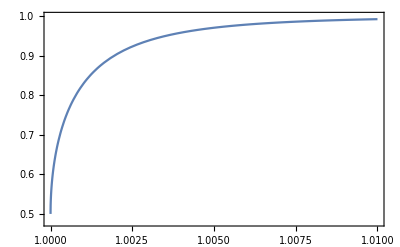

```mathematica
(*--------------------------------------------------General GHZ for I----------------------------------------------------*)
Clear[rou,rouI,rouIII,rouIB,rouIIIB,rouIC,rouIIIC,eigRouIB,eigRouIC,eigRouIBpIC,eigRouIII,detI,eigIpIIBC,a,b,g,r,state];a = 1/(√2); b =a; g=a;o=50;
state[a_,b_,g_, o_, r_] =({{a c[o,r], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b, a s[o,r], 0, 0, 0}});
rou[a_,b_,g_, o_, r_] = KroneckerProduct[state[a,b,g,o,r],Transpose[state[a,b,g,o,r]]];
rouIIIB[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rou[a,b,g,o,r],{2,2}] ,{2}]];
rouIB[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIB[a,b,g,o,r][[1;;2,1;;2]]+rouIIIB[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIB[a,b,g,o,r][[1;;2,5;;6]]+rouIIIB[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIB[a,b,g,o,r][[5;;6,1;;2]]+rouIIIB[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIB[a,b,g,o,r][[5;;6,5;;6]]+rouIIIB[a,b,g,o,r][[7;;8,7;;8]]),2]]];
"rouIII is :"
rouIII[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIIIB[a,b,g,o,r],{2,2}] ,{2}]] 
rouI[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIII[a,b,g,o,r],{2,2}] ,{2}]];
rouIIIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rou[a,b,g,o,r][[1;;2,1;;2]]+rou[a,b,g,o,r][[3;;4,3;;4]]),
(rou[a,b,g,o,r][[1;;2,5;;6]]+rou[a,b,g,o,r][[3;;4,7;;8]]),
(rou[a,b,g,o,r][[1;;2,9;;10]]+rou[a,b,g,o,r][[3;;4,11;;12]]),(rou[a,b,g,o,r][[1;;2,13;;14]]+rou[a,b,g,o,r][[3;;4,15;;16]]),2],
Join[(rou[a,b,g,o,r][[5;;6,1;;2]]+rou[a,b,g,o,r][[7;;8,3;;4]]),
(rou[a,b,g,o,r][[5;;6,5;;6]]+rou[a,b,g,o,r][[7;;8,7;;8]]),
(rou[a,b,g,o,r][[5;;6,9;;10]]+rou[a,b,g,o,r][[7;;8,11;;12]]),(rou[a,b,g,o,r][[5;;6,13;;14]]+rou[a,b,g,o,r][[7;;8,15;;16]]),2],
Join[(rou[a,b,g,o,r][[9;;10,1;;2]]+rou[a,b,g,o,r][[11;;12,3;;4]]),
(rou[a,b,g,o,r][[9;;10,5;;6]]+rou[a,b,g,o,r][[11;;12,7;;8]]),
(rou[a,b,g,o,r][[9;;10,9;;10]]+rou[a,b,g,o,r][[11;;12,11;;12]]),(rou[a,b,g,o,r][[9;;10,13;;14]]+rou[a,b,g,o,r][[11;;12,15;;16]]),2],
Join[(rou[a,b,g,o,r][[13;;14,1;;2]]+rou[a,b,g,o,r][[15;;16,3;;4]]),
(rou[a,b,g,o,r][[13;;14,5;;6]]+rou[a,b,g,o,r][[15;;16,7;;8]]),
(rou[a,b,g,o,r][[13;;14,9;;10]]+rou[a,b,g,o,r][[15;;16,11;;12]]),(rou[a,b,g,o,r][[13;;14,13;;14]]+rou[a,b,g,o,r][[15;;16,15;;16]]),2]]];
rouIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIC[a,b,g,o,r][[1;;2,1;;2]]+rouIIIC[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIC[a,b,g,o,r][[1;;2,5;;6]]+rouIIIC[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIC[a,b,g,o,r][[5;;6,1;;2]]+rouIIIC[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIC[a,b,g,o,r][[5;;6,5;;6]]+rouIIIC[a,b,g,o,r][[7;;8,7;;8]]),2]]];

Clear[r];
eigRouIB[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIB[a,b,g,o,r].sig22.rouIB[a,b,g,o,r].sig22]];
eigRouIC[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIC[a,b,g,o,r].sig22.rouIC[a,b,g,o,r].sig22]];
eigRouIBpIC[a_,b_,g_, o_, r_] = Simplify[eigRouIB[a,b,g,o,r]+eigRouIC[a,b,g,o,r]];
"eigRouIII is :"
eigRouIII[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIII[a,b,g,o,r].sig22.rouIII[a,b,g,o,r].sig22]]
detI[a_,b_,g_, o_, r_] = Simplify[Det[rouI[a,b,g,o,r]]];
eigIpIIBC[a_,b_,g_,o_,r_] = 4*detI[a,b,g,o,r]-2*(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2-eigRouIII[a,b,g,o,r][[4]];

r=1.0;
"detI is :"  
detI[a,b,g,o,r]
"IB is :"
N[(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2]
"IC is :"
N[(Sqrt[eigRouIC[a,b,g,o,r][[1]]]-Sqrt[eigRouIC[a,b,g,o,r][[2]]]-Sqrt[eigRouIC[a,b,g,o,r][[3]]]-Sqrt[eigRouIC[a,b,g,o,r][[4]]])^2]
"III is :"
eigRouIII[a,b,g,o,r][[4]]
"total is :"
N[eigIpIIBC[a,b,g,o,r]]

Clear[r];
Plot[{eigIpIIBC[a,b,g,50,r]},{r,1.,1.01},Frame->True,PlotRange->{0.48,1}](*
Plot[{eigIpIIBC[a,b,g,15,r]},{r,1.0001,1.01}]
Plot[{eigIpIIBC[a,b,g,30,r]},{r,1.0001,1.01}]
Plot[{eigIpIIBC[a,b,g,50,r]},{r,1.0001,1.01}]*)
```

detB is :

1/4

IB is :

0.

IIB is :

0.

BC is:

0

total is :

1.

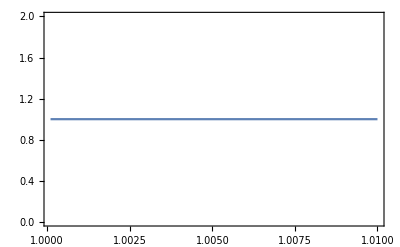

```mathematica
(*----------------------------------------------General GHZ for B--------------------------------------------*)
Clear[rouIIB,rouIIBC,rouBC,rouB,eigRouIIB,eigRouBC,detB,eigBpIIIC,a,b,g,o,r];a = 1/(√2); b =a; g=a;o=50;
rouIIB[a_,b_,g_, o_, r_] = rouIIIB[a,b,g, o, r] [[1;;4,1;;4]]+rouIIIB[a,b,g,o,r] [[5;;8,5;;8]];
rouIIBC[a_,b_,g_, o_, r_] = rou[a,b,g, o, r] [[1;;8,1;;8]]+rou[a,b,g,o,r] [[9;;16,9;;16]];
(*"rouBC is :"*)
rouBC[a_,b_,g_, o_, r_] = Simplify[rouIIBC[a,b,g, o, r] [[1;;4,1;;4]]+rouIIBC[a,b,g,o,r] [[5;;8,5;;8]]];
(*"rouB is :"*)
rouB[a_,b_,g_, o_, r_] = Simplify[rouIIB[a,b,g, o, r] [[1;;2,1;;2]]+rouIIB[a,b,g,o,r] [[3;;4,3;;4]]];

eigRouIIB[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIIB[a,b,g,o,r].sig22.rouIIB[a,b,g,o,r].sig22]];
(*"eigRouBC is "*)
eigRouBC[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouBC[a,b,g,o,r].sig22.rouBC[a,b,g,o,r].sig22]];
detB[a_,b_,g_, o_, r_] =  Simplify[Det[rouB[a,b,g,o,r]]];
eigBpIIIC[a_,b_,g_,o_,r_] = 4*detB[a,b,g,o,r]-(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2-(Sqrt[eigRouIIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIIB[a,b,g,o,r][[4]]])^2;

r=1.;
"detB is :"
detB[a,b,g,o,r]
"IB is :"
N[(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2]
"IIB is :"
N[(Sqrt[eigRouIIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIIB[a,b,g,o,r][[4]]])^2]
"BC is:"
eigRouBC[a,b,g,o,r][[1]]-eigRouBC[a,b,g,o,r][[2]]
"total is :"
N[eigBpIIIC[a,b,g,o,r]]
Clear[r];
Plot[{eigBpIIIC[a,b,g,50,r]},{r,1.0001,1.01},Frame->True]
```

tauIB is :

0.0190637

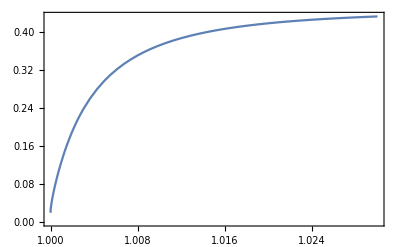

detI is :

0.222222

IB is :

0.0190637

IC is :

0.0190637

III is :

0.444444

total is :

0.406317

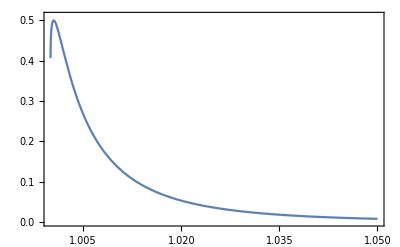

```mathematica
(*------------------------------------------------General W for I--------------------------------------------------*)
Clear[rou,rouI,rouIB,rouIII,rouIIIB,rouIIIC,rouIC,eigRouIB,eigRouIC,eigRouIII,detI,tauIB,tauIC,eigIpIIBC,a,b,g,r,state];a = 1/(√3); b =a; g=a;o=50;Clear[r];
state[a_,b_,g_, o_, r_] =({{0, a c[o,r], b c[o,r], 0, 0, 0, 0, 0, g, 0, 0, 0, 0, a s[o,r], b s[o,r], 0}});
rou[a_,b_,g_, o_, r_] = KroneckerProduct[state[a,b,g,o,r],Transpose[state[a,b,g,o,r]]];
rouIIIB[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rou[a,b,g,o,r],{2,2}] ,{2}]];
rouIB[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIB[a,b,g,o,r][[1;;2,1;;2]]+rouIIIB[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIB[a,b,g,o,r][[1;;2,5;;6]]+rouIIIB[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIB[a,b,g,o,r][[5;;6,1;;2]]+rouIIIB[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIB[a,b,g,o,r][[5;;6,5;;6]]+rouIIIB[a,b,g,o,r][[7;;8,7;;8]]),2]]];
(*"rouIII is :"*)
rouIII[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIIIB[a,b,g,o,r],{2,2}] ,{2}]];
(*"rouI is :"*)
rouI[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIII[a,b,g,o,r],{2,2}] ,{2}]];
rouIIIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rou[a,b,g,o,r][[1;;2,1;;2]]+rou[a,b,g,o,r][[3;;4,3;;4]]),
(rou[a,b,g,o,r][[1;;2,5;;6]]+rou[a,b,g,o,r][[3;;4,7;;8]]),
(rou[a,b,g,o,r][[1;;2,9;;10]]+rou[a,b,g,o,r][[3;;4,11;;12]]),(rou[a,b,g,o,r][[1;;2,13;;14]]+rou[a,b,g,o,r][[3;;4,15;;16]]),2],
Join[(rou[a,b,g,o,r][[5;;6,1;;2]]+rou[a,b,g,o,r][[7;;8,3;;4]]),
(rou[a,b,g,o,r][[5;;6,5;;6]]+rou[a,b,g,o,r][[7;;8,7;;8]]),
(rou[a,b,g,o,r][[5;;6,9;;10]]+rou[a,b,g,o,r][[7;;8,11;;12]]),(rou[a,b,g,o,r][[5;;6,13;;14]]+rou[a,b,g,o,r][[7;;8,15;;16]]),2],
Join[(rou[a,b,g,o,r][[9;;10,1;;2]]+rou[a,b,g,o,r][[11;;12,3;;4]]),
(rou[a,b,g,o,r][[9;;10,5;;6]]+rou[a,b,g,o,r][[11;;12,7;;8]]),
(rou[a,b,g,o,r][[9;;10,9;;10]]+rou[a,b,g,o,r][[11;;12,11;;12]]),(rou[a,b,g,o,r][[9;;10,13;;14]]+rou[a,b,g,o,r][[11;;12,15;;16]]),2],
Join[(rou[a,b,g,o,r][[13;;14,1;;2]]+rou[a,b,g,o,r][[15;;16,3;;4]]),
(rou[a,b,g,o,r][[13;;14,5;;6]]+rou[a,b,g,o,r][[15;;16,7;;8]]),
(rou[a,b,g,o,r][[13;;14,9;;10]]+rou[a,b,g,o,r][[15;;16,11;;12]]),(rou[a,b,g,o,r][[13;;14,13;;14]]+rou[a,b,g,o,r][[15;;16,15;;16]]),2]]];
rouIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIC[a,b,g,o,r][[1;;2,1;;2]]+rouIIIC[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIC[a,b,g,o,r][[1;;2,5;;6]]+rouIIIC[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIC[a,b,g,o,r][[5;;6,1;;2]]+rouIIIC[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIC[a,b,g,o,r][[5;;6,5;;6]]+rouIIIC[a,b,g,o,r][[7;;8,7;;8]]),2]]];


(*"eigRouIB is :"*)
eigRouIB[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIB[a,b,g,o,r].sig22.rouIB[a,b,g,o,r].sig22]];
eigRouIC[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIC[a,b,g,o,r].sig22.rouIC[a,b,g,o,r].sig22]];
eigRouIBpIC[a_,b_,g_, o_, r_] = Simplify[eigRouIB[a,b,g,o,r]+eigRouIC[a,b,g,o,r]];
(*"eigRouIII is :"*)
eigRouIII[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIII[a,b,g,o,r].sig22.rouIII[a,b,g,o,r].sig22]];
detI[a_,b_,g_, o_, r_] = Simplify[Det[rouI[a,b,g,o,r]]];
"tauIB is :"
tauIB[a_,b_,g_, o_, r_] :=(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2
N[tauIB[a,b,g,o,1]]
Plot[tauIB[a,b,g,o,r],{r,1,1.03},Frame->True]
tauIC[a_,b_,g_, o_, r_] :=
(Sqrt[eigRouIC[a,b,g,o,r][[1]]]-Sqrt[eigRouIC[a,b,g,o,r][[2]]]-Sqrt[eigRouIC[a,b,g,o,r][[3]]]-Sqrt[eigRouIC[a,b,g,o,r][[4]]])^2
eigIpIIBC[a_,b_,g_,o_,r_] := 4*detI[a,b,g,o,r]-2*tauIB[a,b,g,o,r]-eigRouIII[a,b,g,o,r][[4]];

a = 1/(√3); b =a; g=a;o=50;r=1.0;
"detI is :"  
detI[a,b,g,o,r]
"IB is :"
N[tauIB[a,b,g,o,r]]
"IC is :"
N[tauIC[a,b,g,o,r]]
"III is :"
eigRouIII[a,b,g,o,r][[4]]
"total is :"
N[eigIpIIBC[a,b,g,o,r]]

Clear[r];
Plot[{eigIpIIBC[a,b,g,10,r]},{r,1,1.05},Frame->True,PlotRange->{0.,0.51}]
```

detB is :

0.222222

IB is :

0.0190637

IIB is :

0.0190637

BC is:

0.444444

total is :

0.406317

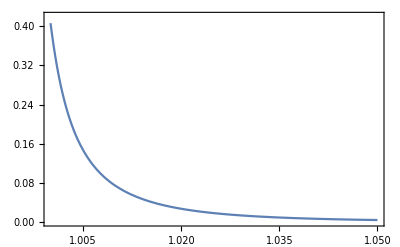

```mathematica
(*----------------------------------------------General W for B--------------------------------------------*)
Clear[rouIIB,rouIIBC,rouBC,rouB,eigRouIIB,eigRouBC,detB,eigBpIIIC,tauIB,tauIIB,a,b,g,o,r];a = 1/(√3); b =a; g=a;o=50;Clear[r];
rouIIB[a_,b_,g_,o_,r_] = rouIIIB[a,b,g,o,r] [[1;;4,1;;4]]+rouIIIB[a,b,g,o,r] [[5;;8,5;;8]];
rouIIBC[a_,b_,g_,o_,r_] = rou[a,b,g, o, r] [[1;;8,1;;8]]+rou[a,b,g,o,r] [[9;;16,9;;16]];
rouBC[a_,b_,g_, o_, r_] = rouIIBC[a,b,g, o, r] [[1;;4,1;;4]]+rouIIBC[a,b,g,o,r] [[5;;8,5;;8]];
rouB[a_,b_,g_, o_, r_] = rouIIB[a,b,g, o, r] [[1;;2,1;;2]]+rouIIB[a,b,g,o,r] [[3;;4,3;;4]];

eigRouIIB[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIIB[a,b,g,o,r].sig22.rouIIB[a,b,g,o,r].sig22]];
(*"eigRouBC is "*)
eigRouBC[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouBC[a,b,g,o,r].sig22.rouBC[a,b,g,o,r].sig22]]
detB[a_,b_,g_, o_, r_] =  Simplify[Det[rouB[a,b,g,o,r]]];
(*"tauIB is :"*)
tauIB[a_,b_,g_, o_, r_] :=(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2
tauIIB[a_,b_,g_, o_, r_] :=
(Sqrt[eigRouIIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIIB[a,b,g,o,r][[4]]])^2;
eigBpIIIC[a_,b_,g_,o_,r_] := 4*detB[a,b,g,o,r]-tauIB[a,b,g,o,r]-tauIIB[a,b,g,o,r]-eigRouBC[a,b,g,o,r][[1]];

r=1.0;
"detB is :"
N[detB[a,b,g,o,r]]
"IB is :"
N[tauIB[a,b,g,o,r]]
"IIB is :"
N[tauIIB[a,b,g,o,r]]
"BC is:"
N[eigRouBC[a,b,g,o,r][[1]]]
"total is :"
N[eigBpIIIC[a,b,g,o,r]]


Plot[{eigBpIIIC[a,b,g,10,r]},{r,1.,1.05},Frame->True,PlotRange->{0,0.42}]
```

tauIB is :

0.25

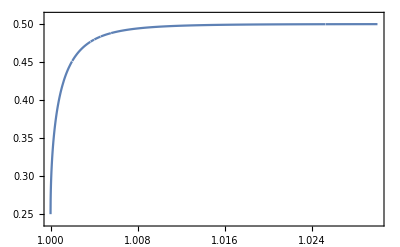

detI is :

0.1875

IB is :

0.25

IC is :

0.25

III is :

0.25

total is :

0.

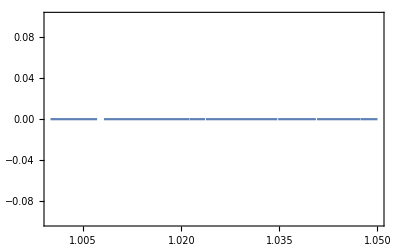

```mathematica
(*------------------------------------------------Max W for I--------------------------------------------------*)
Clear[rou,rouI,rouIB,rouIII,rouIIIB,rouIIIC,rouIC,eigRouIB,eigRouIC,eigRouIII,detI,tauIB,tauIC,eigIpIIBC,a,b,g,r,state];a = 1/(√2); b =0; g=1/2;o=50;Clear[r];
state[a_,b_,g_, o_, r_] =({{a c[o,r], 0, 0, 0, 0, 0, 0, 0, 0, g, g, 0, a s[o,r], 0, 0, 0}});
rou[a_,b_,g_, o_, r_] = KroneckerProduct[state[a,b,g,o,r],Transpose[state[a,b,g,o,r]]];
rouIIIB[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rou[a,b,g,o,r],{2,2}] ,{2}]];
rouIB[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIB[a,b,g,o,r][[1;;2,1;;2]]+rouIIIB[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIB[a,b,g,o,r][[1;;2,5;;6]]+rouIIIB[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIB[a,b,g,o,r][[5;;6,1;;2]]+rouIIIB[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIB[a,b,g,o,r][[5;;6,5;;6]]+rouIIIB[a,b,g,o,r][[7;;8,7;;8]]),2]]];
(*"rouIII is :"*)
rouIII[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIIIB[a,b,g,o,r],{2,2}] ,{2}]];
(*"rouI is :"*)
rouI[a_,b_,g_, o_, r_] = Simplify[Map[Tr,Partition[rouIII[a,b,g,o,r],{2,2}] ,{2}]];
rouIIIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rou[a,b,g,o,r][[1;;2,1;;2]]+rou[a,b,g,o,r][[3;;4,3;;4]]),
(rou[a,b,g,o,r][[1;;2,5;;6]]+rou[a,b,g,o,r][[3;;4,7;;8]]),
(rou[a,b,g,o,r][[1;;2,9;;10]]+rou[a,b,g,o,r][[3;;4,11;;12]]),(rou[a,b,g,o,r][[1;;2,13;;14]]+rou[a,b,g,o,r][[3;;4,15;;16]]),2],
Join[(rou[a,b,g,o,r][[5;;6,1;;2]]+rou[a,b,g,o,r][[7;;8,3;;4]]),
(rou[a,b,g,o,r][[5;;6,5;;6]]+rou[a,b,g,o,r][[7;;8,7;;8]]),
(rou[a,b,g,o,r][[5;;6,9;;10]]+rou[a,b,g,o,r][[7;;8,11;;12]]),(rou[a,b,g,o,r][[5;;6,13;;14]]+rou[a,b,g,o,r][[7;;8,15;;16]]),2],
Join[(rou[a,b,g,o,r][[9;;10,1;;2]]+rou[a,b,g,o,r][[11;;12,3;;4]]),
(rou[a,b,g,o,r][[9;;10,5;;6]]+rou[a,b,g,o,r][[11;;12,7;;8]]),
(rou[a,b,g,o,r][[9;;10,9;;10]]+rou[a,b,g,o,r][[11;;12,11;;12]]),(rou[a,b,g,o,r][[9;;10,13;;14]]+rou[a,b,g,o,r][[11;;12,15;;16]]),2],
Join[(rou[a,b,g,o,r][[13;;14,1;;2]]+rou[a,b,g,o,r][[15;;16,3;;4]]),
(rou[a,b,g,o,r][[13;;14,5;;6]]+rou[a,b,g,o,r][[15;;16,7;;8]]),
(rou[a,b,g,o,r][[13;;14,9;;10]]+rou[a,b,g,o,r][[15;;16,11;;12]]),(rou[a,b,g,o,r][[13;;14,13;;14]]+rou[a,b,g,o,r][[15;;16,15;;16]]),2]]];
rouIC[a_,b_,g_, o_, r_] = Simplify[Join[
Join[(rouIIIC[a,b,g,o,r][[1;;2,1;;2]]+rouIIIC[a,b,g,o,r][[3;;4,3;;4]]),(rouIIIC[a,b,g,o,r][[1;;2,5;;6]]+rouIIIC[a,b,g,o,r][[3;;4,7;;8]]),2],Join[(rouIIIC[a,b,g,o,r][[5;;6,1;;2]]+rouIIIC[a,b,g,o,r][[7;;8,3;;4]]),(rouIIIC[a,b,g,o,r][[5;;6,5;;6]]+rouIIIC[a,b,g,o,r][[7;;8,7;;8]]),2]]];


(*"eigRouIB is :"*)
eigRouIB[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIB[a,b,g,o,r].sig22.rouIB[a,b,g,o,r].sig22]];
eigRouIC[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIC[a,b,g,o,r].sig22.rouIC[a,b,g,o,r].sig22]];
eigRouIBpIC[a_,b_,g_, o_, r_] = Simplify[eigRouIB[a,b,g,o,r]+eigRouIC[a,b,g,o,r]];
(*"eigRouIII is :"*)
eigRouIII[a_,b_,g_, o_, r_] = Simplify[Eigenvalues[rouIII[a,b,g,o,r].sig22.rouIII[a,b,g,o,r].sig22]];
detI[a_,b_,g_, o_, r_] = Simplify[Det[rouI[a,b,g,o,r]]];
"tauIB is :"
tauIB[a_,b_,g_, o_, r_] :=(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2
N[tauIB[a,b,g,o,1]]
Plot[tauIB[a,b,g,o,r],{r,1,1.03},Frame->True,PlotRange->{0.24,0.51}]
tauIC[a_,b_,g_, o_, r_] :=
(Sqrt[eigRouIC[a,b,g,o,r][[1]]]-Sqrt[eigRouIC[a,b,g,o,r][[2]]]-Sqrt[eigRouIC[a,b,g,o,r][[3]]]-Sqrt[eigRouIC[a,b,g,o,r][[4]]])^2
eigIpIIBC[a_,b_,g_,o_,r_] := 4*detI[a,b,g,o,r]-2*tauIB[a,b,g,o,r]-eigRouIII[a,b,g,o,r][[4]];

a = 1/(√3); b =a; g=a;o=50;r=1.0;
"detI is :"  
detI[a,b,g,o,r]
"IB is :"
N[tauIB[a,b,g,o,r]]
"IC is :"
N[tauIC[a,b,g,o,r]]
"III is :"
eigRouIII[a,b,g,o,r][[4]]
"total is :"
N[eigIpIIBC[a,b,g,o,r]]

Clear[r];
Plot[{eigIpIIBC[a,b,g,10,r]},{r,1,1.05},Frame->True,PlotRange->{-0.1,0.1}]
```

detB is :

0.1875

IB is :

0.25

IIB is :

0.25

BC is:

0.25

total is :

5.55112×10^-17

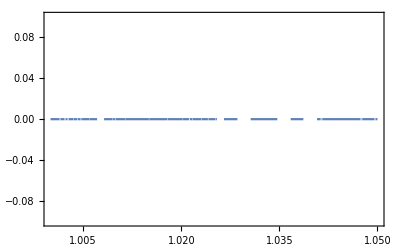

```mathematica
(*----------------------------------------------Max W for B--------------------------------------------*)
Clear[rouIIB,rouIIBC,rouBC,rouB,eigRouIIB,eigRouBC,detB,eigBpIIIC,tauIB,tauIIB,a,b,g,o,r];a = 1/(√2); b =0; g=1/2;o=50;Clear[r];
rouIIB[a_,b_,g_,o_,r_] = rouIIIB[a,b,g,o,r] [[1;;4,1;;4]]+rouIIIB[a,b,g,o,r] [[5;;8,5;;8]];
rouIIBC[a_,b_,g_,o_,r_] = rou[a,b,g, o, r] [[1;;8,1;;8]]+rou[a,b,g,o,r] [[9;;16,9;;16]];
rouBC[a_,b_,g_, o_, r_] = rouIIBC[a,b,g, o, r] [[1;;4,1;;4]]+rouIIBC[a,b,g,o,r] [[5;;8,5;;8]];
rouB[a_,b_,g_, o_, r_] = rouIIB[a,b,g, o, r] [[1;;2,1;;2]]+rouIIB[a,b,g,o,r] [[3;;4,3;;4]];

eigRouIIB[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouIIB[a,b,g,o,r].sig22.rouIIB[a,b,g,o,r].sig22]];
(*"eigRouBC is "*)
eigRouBC[a_,b_,g_, o_, r_] := Simplify[Eigenvalues[rouBC[a,b,g,o,r].sig22.rouBC[a,b,g,o,r].sig22]]
detB[a_,b_,g_, o_, r_] =  Simplify[Det[rouB[a,b,g,o,r]]];
(*"tauIB is :"*)
tauIB[a_,b_,g_, o_, r_] :=(Sqrt[eigRouIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIB[a,b,g,o,r][[4]]])^2
tauIIB[a_,b_,g_, o_, r_] :=
(Sqrt[eigRouIIB[a,b,g,o,r][[1]]]-Sqrt[eigRouIIB[a,b,g,o,r][[2]]]-Sqrt[eigRouIIB[a,b,g,o,r][[3]]]-Sqrt[eigRouIIB[a,b,g,o,r][[4]]])^2;
eigBpIIIC[a_,b_,g_,o_,r_] := 4*detB[a,b,g,o,r]-tauIB[a,b,g,o,r]-tauIIB[a,b,g,o,r]-eigRouBC[a,b,g,o,r][[1]];

r=1.0;
"detB is :"
N[detB[a,b,g,o,r]]
"IB is :"
N[tauIB[a,b,g,o,r]]
"IIB is :"
N[tauIIB[a,b,g,o,r]]
"BC is:"
N[eigRouBC[a,b,g,o,r][[1]]]
"total is :"
N[eigBpIIIC[a,b,g,o,r]]


Plot[{eigBpIIIC[a,b,g,10,r]},{r,1.,1.05},Frame->True,PlotRange->{-0.1,0.1}]
```

```mathematica
Clear[maxE,AB,AC];
maxE = ({{1/4, 0, 0, 0}, {0, 1/4, 0, 0}, {0, 0, 1/4, 0}, {0, 0, 0, 1/4}}); AB = ({{1/2, 0, 0, 1/2}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1/2, 0, 0, 1/2}});AC = ({{1/2, 0, 1/2, 0}, {0, 0, 0, 0}, {1/2, 0, 1/2, 0}, {0, 0, 0, 0}});
Simplify[Eigenvalues[maxE.sig22.maxE.sig22]]
Simplify[Eigenvalues[AB.sig22.AB.sig22]]
Simplify[Eigenvalues[AC.sig22.AC.sig22]]
Clear[maxE,AB,AC];
```

{1/16,1/16,1/16,1/16}

{1,0,0,0}

{0,0,0,0}